```mathematica
ClearAll["Global`*"];
SeedRandom[];

(* ==========================================================*)
(*1. 并发暴胀引擎 (完全原生 Union 去重，无人工排序干预)*)
(* ==========================================================*)
StepEvolution[g_Graph,window_]:=Module[{allEdges,activeEdges,nActive,usedEdges,updates,tempE1,tempE2,x,y,z,wCounter,newVertices,newActive,newFrozen,remainingEdges},allEdges=EdgeList[g];
activeEdges=RandomSample[Cases[allEdges,_UndirectedEdge]];
nActive=Length[activeEdges];
If[nActive<2,Return[{g,0}]];
usedEdges={};updates={};
Do[tempE1=activeEdges[[i]];
If[!MemberQ[usedEdges,tempE1],Do[tempE2=activeEdges[[j]];
If[!MemberQ[usedEdges,tempE2]&&Length[Intersection[List@@tempE1,List@@tempE2]]==1,AppendTo[updates,{tempE1,tempE2}];
AppendTo[usedEdges,tempE1];AppendTo[usedEdges,tempE2];
Break[];],{j,i+1,Min[i+window,nActive]}]],{i,1,nActive}];
If[Length[updates]==0,Return[{g,0}]];
wCounter=Max[VertexList[g]];
newVertices={};newActive={};newFrozen={};
Do[y=Intersection[List@@pair[[1]],List@@pair[[2]]][[1]];
x=Complement[List@@pair[[1]],{y}][[1]];
z=Complement[List@@pair[[2]],{y}][[1]];
wCounter++;
AppendTo[newVertices,wCounter];
newActive=Join[newActive,{UndirectedEdge[x,z],UndirectedEdge[x,wCounter],UndirectedEdge[wCounter,z]}];
newFrozen=Join[newFrozen,{DirectedEdge[x,y],DirectedEdge[y,z]}];,{pair,updates}];
remainingEdges=Complement[allEdges,Flatten[updates]];
{Graph[Union[Join[VertexList[g],newVertices]],Union[Join[remainingEdges,newActive,newFrozen]]],Length[updates]}];

(* ==========================================================*)
(*2. 并发宇宙演化采集 (40 步)*)
(* ==========================================================*)
Print[Style["[1/3] 正在点燃并发暴胀宇宙... (目标: 40步)",Blue,Bold]];
universe=CompleteGraph[6];
steps=100;
widthData={};

Monitor[Do[{universe,concurrentCount}=StepEvolution[universe,100];
If[concurrentCount>0,activeNodes=Union[Flatten[List@@@Cases[EdgeList[universe],_UndirectedEdge]]];
If[Length[activeNodes]>1,dists=(GraphDistance[universe,1,#]&/@activeNodes);
AppendTo[widthData,{i,StandardDeviation[Select[dists,NumericQ]]}];];];,{i,1,steps}],ProgressIndicator[i,{0,steps}]];

(* ==========================================================*)
(*3. 提取最终的能量分布 (形成波包)*)
(* ==========================================================*)
Print[Style["[2/3] 宇宙停止暴胀，正在扫描空间前沿能量分布...",Blue,Bold]];

finalActiveNodes=Union[Flatten[List@@@Cases[EdgeList[universe],_UndirectedEdge]]];
finalDists=Select[(GraphDistance[universe,1,#]&/@finalActiveNodes),NumericQ];

plotWavePacket=Histogram[finalDists,Automatic,"ProbabilityDensity",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Topological Distance (r)","Energy Density"},PlotLabel->Style["Wave Packet Energy Distribution",14,Bold],GridLines->{Automatic,Automatic},ImageSize->450];

(* ==========================================================*)
(*4. 离散对数周期色散检验 (残差雪花)*)
(* ==========================================================*)
Print[Style["[3/3] 正在执行离散色散拟合...",Blue,Bold]];

If[Length[widthData]>20,cutoffStep=10;
adultData=Select[widthData,#[[1]]>cutoffStep&];
w0Init=adultData[[1,2]];
discreteModel=Sqrt[w0^2+(k*t^alpha)^2]*(1+a*Sin[omega*Log[t]+phi]);
nlmDiscrete=Check[NonlinearModelFit[adultData,{discreteModel,k>0&&0.8<alpha<1.2&&a>0},{{w0,w0Init},{k,0.5},{alpha,1.0},{a,0.01},{omega,15},{phi,0}},t,MaxIterations->1500,Method->"NMinimize"],$Failed];
plotSnowflake=If[nlmDiscrete=!=$Failed,r2=nlmDiscrete["RSquared"];
residuals=nlmDiscrete["FitResiduals"];
ListPlot[residuals,PlotStyle->{Red,PointSize[0.025]},Frame->True,FrameLabel->{"Concurrent Steps","Residual Error"},PlotLabel->Style["Discrete Parallel Residuals",14,Bold],Epilog->{Text[Style["\!\(\*SuperscriptBox[\(R\), \(2\)]\) = "<>ToString[NumberForm[r2,{5,6}]],Black,12],{Length[adultData]*0.7,Max[residuals]*0.8}]},GridLines->{None,{0}},ImageSize->450],Graphics[{Text["Fit Failed"]},ImageSize->450]];
Print[Rasterize[Grid[{{plotWavePacket,plotSnowflake}},Spacings->{2,0}],ImageResolution->100]];,Print["数据不足。"]];
```

[1/3] 正在点燃并发暴胀宇宙... (目标: 40步)

[2/3] 宇宙停止暴胀，正在扫描空间前沿能量分布...

[3/3] 正在执行离散色散拟合...

-Graphics-

```mathematica
ClearAll["Global`*"];
SeedRandom[777];

(* ==========================================================*)
(*1. 并发暴胀引擎 (完全原生 Union 去重，无人工排序干预)*)
(* ==========================================================*)
StepEvolution[g_Graph,window_]:=Module[{allEdges,activeEdges,nActive,usedEdges,updates,tempE1,tempE2,x,y,z,wCounter,newVertices,newActive,newFrozen,remainingEdges},allEdges=EdgeList[g];
activeEdges=RandomSample[Cases[allEdges,_UndirectedEdge]];
nActive=Length[activeEdges];
If[nActive<2,Return[{g,0}]];
usedEdges={};updates={};
Do[tempE1=activeEdges[[i]];
If[!MemberQ[usedEdges,tempE1],Do[tempE2=activeEdges[[j]];
If[!MemberQ[usedEdges,tempE2]&&Length[Intersection[List@@tempE1,List@@tempE2]]==1,AppendTo[updates,{tempE1,tempE2}];
AppendTo[usedEdges,tempE1];AppendTo[usedEdges,tempE2];
Break[];],{j,i+1,Min[i+window,nActive]}]],{i,1,nActive}];
If[Length[updates]==0,Return[{g,0}]];
wCounter=Max[VertexList[g]];
newVertices={};newActive={};newFrozen={};
Do[y=Intersection[List@@pair[[1]],List@@pair[[2]]][[1]];
x=Complement[List@@pair[[1]],{y}][[1]];
z=Complement[List@@pair[[2]],{y}][[1]];
wCounter++;
AppendTo[newVertices,wCounter];
newActive=Join[newActive,{UndirectedEdge[x,z],UndirectedEdge[x,wCounter],UndirectedEdge[wCounter,z]}];
newFrozen=Join[newFrozen,{DirectedEdge[x,y],DirectedEdge[y,z]}];,{pair,updates}];
remainingEdges=Complement[allEdges,Flatten[updates]];
{Graph[Union[Join[VertexList[g],newVertices]],Union[Join[remainingEdges,newActive,newFrozen]]],Length[updates]}];

(* ==========================================================*)
(*2. 并发宇宙演化采集 (40 步)*)
(* ==========================================================*)
Print[Style["[1/3] 正在点燃并发暴胀宇宙... (目标: 40步)",Blue,Bold]];
universe=CompleteGraph[6];
steps=400;
widthData={};

Monitor[Do[{universe,concurrentCount}=StepEvolution[universe,70];
If[concurrentCount>0,activeNodes=Union[Flatten[List@@@Cases[EdgeList[universe],_UndirectedEdge]]];
If[Length[activeNodes]>1,dists=(GraphDistance[universe,1,#]&/@activeNodes);
AppendTo[widthData,{i,StandardDeviation[Select[dists,NumericQ]]}];];];,{i,1,steps}],ProgressIndicator[i,{0,steps}]];

(* ==========================================================*)
(*3. 提取最终的能量分布 (形成波包)*)
(* ==========================================================*)
Print[Style["[2/3] 宇宙停止暴胀，正在扫描空间前沿能量分布...",Blue,Bold]];

finalActiveNodes=Union[Flatten[List@@@Cases[EdgeList[universe],_UndirectedEdge]]];
finalDists=Select[(GraphDistance[universe,1,#]&/@finalActiveNodes),NumericQ];

plotWavePacket=Histogram[finalDists,Automatic,"ProbabilityDensity",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Topological Distance (r)","Energy Density"},PlotLabel->Style["Wave Packet Energy Distribution",14,Bold],GridLines->{Automatic,Automatic},ImageSize->450];

(* ==========================================================*)
(*4. 离散对数周期色散检验 (残差雪花)*)
(* ==========================================================*)
Print[Style["[3/3] 正在执行离散色散拟合...",Blue,Bold]];

If[Length[widthData]>20,cutoffStep=10;
adultData=Select[widthData,#[[1]]>cutoffStep&];
w0Init=adultData[[1,2]];
discreteModel=Sqrt[w0^2+(k*t^alpha)^2]*(1+a*Sin[omega*Log[t]+phi]);
nlmDiscrete=Check[NonlinearModelFit[adultData,{discreteModel,k>0&&0.8<alpha<1.2&&a>0},{{w0,w0Init},{k,0.5},{alpha,1.0},{a,0.01},{omega,15},{phi,0}},t,MaxIterations->1500,Method->"NMinimize"],$Failed];
plotSnowflake=If[nlmDiscrete=!=$Failed,r2=nlmDiscrete["RSquared"];
residuals=nlmDiscrete["FitResiduals"];
ListPlot[residuals,PlotStyle->{Red,PointSize[0.025]},Frame->True,FrameLabel->{"Concurrent Steps","Residual Error"},PlotLabel->Style["Discrete Parallel Residuals",14,Bold],Epilog->{Text[Style["\!\(\*SuperscriptBox[\(R\), \(2\)]\) = "<>ToString[NumberForm[r2,{5,6}]],Black,12],{Length[adultData]*0.7,Max[residuals]*0.8}]},GridLines->{None,{0}},ImageSize->450],Graphics[{Text["Fit Failed"]},ImageSize->450]];
Print[Rasterize[Grid[{{plotWavePacket,plotSnowflake}},Spacings->{2,0}],ImageResolution->100]];,Print["数据不足。"]];
```

[1/3] 正在点燃并发暴胀宇宙... (目标: 40步)

[2/3] 宇宙停止暴胀，正在扫描空间前沿能量分布...

[3/3] 正在执行离散色散拟合...

-Graphics-

FittedModel::constr: 属性值 {ParameterTable} 假定的是一个非约束模型. 这些属性的结果可能不是有效的，尤其当拟合参数接近一个约束边界的时候.

| Estimate | Standard Error | t-Statistic | P-Value
w0 | 0.155284 | 2.28237 | 0.0680363 | 0.945792
k | 0.00033765 | 0.00611355 | 0.0552297 | 0.955984
alpha | 0.8 | 0.495048 | 1.616 | 0.106915
a | 14.0545 | 222.346 | 0.0632098 | 0.949632
omega | 0.230689 | 0.174166 | 1.32454 | 0.186113
phi | 12.5902 | 0.933387 | 13.4888 | 3.25288×10^-34

```mathematica
Print[Style["当前撞墙状态下的 R^2 = ",Red,Bold],nlmDiscrete["RSquared"]]
```

当前撞墙状态下的 R^2 = 0.999992

[1/4] 正在剥离因果方向，构建纯粹的无向拓扑骨架...

[2/4] 正在构建巨型浮点稀疏矩阵 (Kirchhoff Matrix)...

[3/4] 正在对角化本征态，提取宏观极限 (最接近 0 的 500 个能量级)...

Eigenvalues::maxit2: 警告：Arnoldi 算法已经达到最大迭代次数 1000，而没有收敛到指定的容差，但是已经返回了当前最佳计算值. 您可以利用 Method -> {Arnoldi, opts} 使用方法选项来增加基本向量的大小、最大迭代次数、降低容差，或者将估计值作为平移使用，以上方法任选其一都可能有帮助.

[4/4] 正在绘制宇宙的拓扑声纹图...

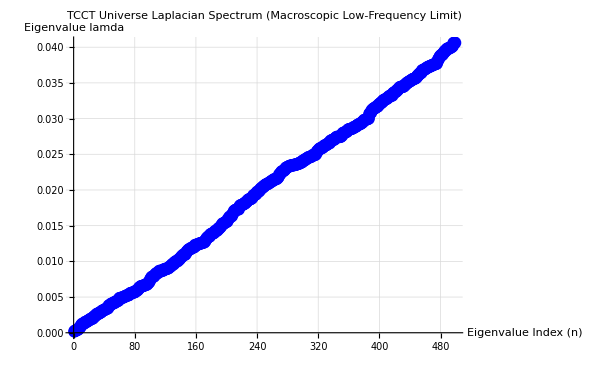

```mathematica
(* ==========================================================*)(*终极拓扑审判：提取 400 步 TCCT 宇宙的拉普拉斯宏观特征谱*)(* ==========================================================*)Print[Style["[1/4] 正在剥离因果方向，构建纯粹的无向拓扑骨架...",Blue,Bold]];
(*将所有边转化为无向边，防止出现虚数特征值*)
undirectedUniverse=Graph[VertexList[universe],UndirectedEdge@@@EdgeList[universe]];

Print[Style["[2/4] 正在构建巨型浮点稀疏矩阵 (Kirchhoff Matrix)...",Blue,Bold]];
(*加 N 强制转换为浮点稀疏矩阵，这是计算 10 万节点不崩的秘诀*)
lapMat=N[KirchhoffMatrix[undirectedUniverse]];

Print[Style["[3/4] 正在对角化本征态，提取宏观极限 (最接近 0 的 500 个能量级)...",Blue,Bold]];
(*-500 表示提取绝对值最小的 500 个特征值*)
eigenVals=Eigenvalues[lapMat,-500];

Print[Style["[4/4] 正在绘制宇宙的拓扑声纹图...",Blue,Bold]];
(*清洗数据：取实部，从小到大排序，剔除绝对零模（孤岛）*)
macroSpectrum=Sort[Select[Re[eigenVals],#>10^-10&]];

(*绘制谱线*)
ListPlot[macroSpectrum,PlotStyle->{Blue,PointSize[0.015]},PlotLabel->Style["TCCT Universe Laplacian Spectrum\n(Macroscopic Low-Frequency Limit)",14,Bold],AxesLabel->{"Eigenvalue Index (n)","Eigenvalue \!\(\*lamda\)"},ImageSize->600,GridLines->Automatic]
```

```mathematica
(*1. 定义桌面绝对路径，彻底绕过 Notebook 路径权限问题*)desktopFileCSV=FileNameJoin[{$HomeDirectory,"Desktop","TCCT_400Steps_Data.csv"}];
desktopFileMX=FileNameJoin[{$HomeDirectory,"Desktop","TCCT_400Steps_Universe.mx"}];

(*2. 导出 CSV (用于阅读和跨平台对比)*)
Export[desktopFileCSV,widthData];

(*3. 导出 MX 二进制快照 (包含整个 universe 图和所有变量，瞬间恢复)*)
DumpSave[desktopFileMX,{universe,widthData,nlmDiscrete}];

Print[Style["🚀 400步数据已成功保存在桌面！",Green,Bold,16]];
Print["1. 统计表: TCCT_400Steps_Data.csv"];
Print["2. 宇宙全状态(二进制): TCCT_400Steps_Universe.mx"];
```

🚀 400步数据已成功保存在桌面！

1. 统计表: TCCT_400Steps_Data.csv

2. 宇宙全状态(二进制): TCCT_400Steps_Universe.mx

```mathematica
(*只显示宽度数据，方便复制*)InputForm[widthData[[All,2]]]
```

{Sqrt[11/26], Sqrt[43/70], 3*Sqrt[2/29], Sqrt[547/110]/3, 2*Sqrt[34/217], 
 Sqrt[3715/4278], Sqrt[5282/4323], Sqrt[49927/8418]/2, Sqrt[32509/85]/16, 
 Sqrt[47449/28815], 15*Sqrt[258/32047], Sqrt[94246/49777], Sqrt[71738/36245], 
 Sqrt[305483/150738], 5*Sqrt[33622/399171], Sqrt[2279107/255783]/2, 
 (2*Sqrt[31011/1081])/7, 6*Sqrt[18138/273707], Sqrt[623837/250809], 
 Sqrt[393493/150447], Sqrt[1916854/79571]/3, Sqrt[501518/185339], 
 Sqrt[10374053/427498]/3, Sqrt[151742/56189], Sqrt[6769534/2458653], 
 5*Sqrt[316466/2816751], 3*Sqrt[166190/527731], Sqrt[5111683/1752314], 
 Sqrt[1925033/161530]/2, Sqrt[25924001/8581970], Sqrt[14626291/58501]/9, 
 21*Sqrt[12174/1716815], Sqrt[8863213/705810]/2, 5*Sqrt[4042/32523], 
 (31*Sqrt[43577/18230])/27, Sqrt[2572417/89441]/3, Sqrt[6416603/217855]/3, 
 Sqrt[27535357/931385]/3, Sqrt[4240921/1285629], Sqrt[9042833/170313]/4, 
 Sqrt[5732227/424222]/2, Sqrt[9193223/2710374], Sqrt[19772337/1449917]/2, 
 2*Sqrt[233771/272305], Sqrt[89445739/6460493]/2, Sqrt[7297181/2090814], 
 11*Sqrt[34718/1193273], Sqrt[54131573/187306]/9, Sqrt[57045682/15851265], 
 Sqrt[5513042/60627]/5, Sqrt[64014919/696318]/5, Sqrt[66942521/18135253], 
 Sqrt[140841335/9509514]/2, Sqrt[49449791/13253110], 4*Sqrt[4885787/20772235], 
 Sqrt[7458761/219234]/3, Sqrt[34387435/567087]/4, 2*Sqrt[11299990/11873193], 
 13*Sqrt[7982/353559], Sqrt[14230374/3692065], Sqrt[5215114/149471]/3, 
 Sqrt[109409282/28023841], Sqrt[114540529/29081751], Sqrt[239299517/60302990], 
 2*Sqrt[3456095/3468539], 8*Sqrt[1012769/16206663], Sqrt[134799387/33673321], 
 (77*Sqrt[23713/1402645])/5, Sqrt[146059351/2264458]/4, Sqrt[15197893/3750213], 
 Sqrt[52943970/12972751], (2*Sqrt[375835/40587])/3, Sqrt[342282043/20773085]/2, 
 Sqrt[354486173/85701306], Sqrt[183033047/44090745], Sqrt[62724731/28569]/23, 
 Sqrt[194216098/46827003], 5*Sqrt[8055403/48240753], Sqrt[69082433/16575126], 
 (9*Sqrt[2630255/141526])/19, Sqrt[220739411/3297633]/4, Sqrt[112983559/27084218], 
 Sqrt[466299173/12384534]/3, 3*Sqrt[13340093/28603778], Sqrt[124240717/29444189], 
 2*Sqrt[31872049/30230753], 4*Sqrt[4096653/15480439], Sqrt[180929743/42544502], 
 2*Sqrt[23146482/21760817], Sqrt[286074121/66961378], Sqrt[291836221/17101014]/2, 
 Sqrt[100377561/5857358]/2, Sqrt[309426673/72150078], Sqrt[106163491/24662510], 
 (9*Sqrt[147233/172466])/4, Sqrt[74786333/1920842]/3, 2*Sqrt[43205026/39869753], 
 2*Sqrt[88687447/81798445], (24*Sqrt[632687/3353791])/5, 
 Sqrt[744378607/10705166]/4, Sqrt[76641266/7953]/47, 6*Sqrt[1560017/12836245], 
 Sqrt[803162747/45883689]/2, 2*Sqrt[51705498/47083613], Sqrt[423430241/10700709]/3, 
 2*Sqrt[4716859/4278845], Sqrt[443684515/25093299]/2, Sqrt[129861087/29333510], 
 Sqrt[232988831/52334373], 7*Sqrt[3249398/35631377], Sqrt[975909607/13629941]/4, 
 Sqrt[3330458/742469], Sqrt[73094734/16237929], Sqrt[34878977/1935607]/2, 
 Sqrt[534075077/1185877]/10, Sqrt[363377983/80554190], Sqrt[557833021/123378486], 
 (2*Sqrt[47415477/5281])/89, 2*Sqrt[72528266/64036005], 9*Sqrt[4867859/87021602], 
 (28*Sqrt[384277/2657063])/5, Sqrt[246385789/54222538], Sqrt[209975089/46006935], 
 Sqrt[321505711/70220210], 2*Sqrt[164609601/143320915], 
 (8*Sqrt[5229962/430967])/13, Sqrt[683580661/148100655], Sqrt[693534253/150207778], 
 Sqrt[157331633/34049170], 3*Sqrt[160282573/311646062], Sqrt[734857633/274803]/24, 
 Sqrt[1493431837/12852942]/5, Sqrt[75933931/4085854]/2, 2*Sqrt[64432509/55337177], 
 49*Sqrt[328261/168664161], 9*Sqrt[19767309/342453530], 2*Sqrt[20404946/17410713], 
 Sqrt[831021862/176973891], Sqrt[35877487/7633626], (7*Sqrt[43979/114630])/2, 
 5*Sqrt[7749505/41137258], (3*Sqrt[16449181/1958491])/4, Sqrt[95041105/5019467]/2, 
 2*Sqrt[12757286/10772071], Sqrt[467149937/98292353], 4*Sqrt[9858395/33188491], 
 Sqrt[1927884797/404874762], Sqrt[979670399/22822894]/3, 
 Sqrt[1985650427/103994105]/2, (2*Sqrt[252124111/23453259])/3, 
 Sqrt[255861618/53460385], Sqrt[71642661/14949478], 2*Sqrt[18859559/15708777], 
 Sqrt[712639497/1483963]/10, Sqrt[27876307/5791715], 3*Sqrt[20404515/38150851], 
 (2*Sqrt[279398657/1916971])/11, Sqrt[1128518389/9374883]/5, 
 2*Sqrt[143313221/118946289], Sqrt[1164152821/240868326], 
 (10*Sqrt[5931691/13605647])/3, Sqrt[399287841/82469630], Sqrt[404716454/83548285], 
 Sqrt[821098991/169252874], Sqrt[415896249/85643482], Sqrt[1266113167/260022610], 
 Sqrt[1281911671/596258]/21, Sqrt[865495835/177277594], Sqrt[50557163/10343186], 
 Sqrt[121004203/6180065]/2, Sqrt[674592007/15292662]/3, 7*Sqrt[1989661/19885529], 
 Sqrt[691083299/625391]/15, Sqrt[2803390745/570326042], 
 3*Sqrt[157828422/288540253], Sqrt[1441387589/1727869]/13, 
 Sqrt[1461717794/32854969]/3, Sqrt[2956223717/7387222]/9, 
 Sqrt[1495786211/302887578], Sqrt[3027045541/613528130], 
 2*Sqrt[191441982/155207993], Sqrt[193973087/4359918]/3, Sqrt[241416965/48824034], 
 Sqrt[1590262315/321222531], Sqrt[357810407/4511199]/4, Sqrt[1631014522/328640703], 
 2*Sqrt[413043418/332368653], Sqrt[3345043987/167903285]/2, 
 Sqrt[3384526499/169774385]/2, Sqrt[3419630027/171446289]/2, 
 Sqrt[864983167/43347410]/2, Sqrt[219319379/1218862]/6, Sqrt[1774073945/354485251], 
 Sqrt[256838577/51235879], Sqrt[907972049/16409]/105, Sqrt[920171255/182959439], 
 Sqrt[930491471/185021205], Sqrt[1879693774/41506679]/3, 
 (5*Sqrt[30398399/465447])/18, Sqrt[106966538/2354605]/3, Sqrt[433468569/85707478], 
 Sqrt[83927887/1842522]/3, Sqrt[1995423862/43775165]/3, Sqrt[504733582/99521359], 
 Sqrt[340208978/67007591], 7*Sqrt[327121/3150134], Sqrt[220588817/10801427]/2, 
 Sqrt[2114181201/103626007]/2, Sqrt[4281962035/209489439]/2, 
 Sqrt[43324301/8467809], Sqrt[2186364866/427211065], Sqrt[552076003/11992345]/3, 
 Sqrt[223017697/43558237], Sqrt[4510302281/97887938]/3, 7*Sqrt[46590398/445974045], 
 Sqrt[2307828727/50048345]/3, Sqrt[777930845/71611]/46, Sqrt[2360372947/5665165]/9, 
 (2*Sqrt[49694135/4294437])/3, (2*Sqrt[201014681/15301])/101, 
 Sqrt[304293191/6560215]/3, Sqrt[2461982287/13258246]/6, 
 Sqrt[2485107806/481539061], (13*Sqrt[29728319/60775667])/4, 
 Sqrt[2540318493/491176153], Sqrt[1710386417/82642881]/2, Sqrt[287846767/55596755], 
 2*Sqrt[328144235/253008789], Sqrt[884296509/170202982], 
 2*Sqrt[669235862/514643403], Sqrt[1352269543/259797983], 
 Sqrt[2730929722/523924635], (2*Sqrt[689780578/2350907])/15, 
 Sqrt[2788248277/59326909]/3, Sqrt[56256693/10774478], Sqrt[1894445747/362153494], 
 2*Sqrt[717467561/548417521], Sqrt[967391042/184576427], 
 Sqrt[2925871894/557830101], (9*Sqrt[1157177/4464946])/2, 
 Sqrt[2982450621/567255403], (8*Sqrt[1423483/693433])/5, 3*Sqrt[17300651/29587870], 
 Sqrt[6122793569/129273110]/3, Sqrt[3088403831/586822411], 
 (5*Sqrt[62253305/32849137])/3, 2*Sqrt[196094359/148958115], 
 (2*Sqrt[66055074/173395])/17, Sqrt[3198464467/606163971], 
 Sqrt[1616871158/306048783], Sqrt[3260621598/616373605], 
 Sqrt[6580981135/19429913]/8, Sqrt[829769587/156720234], 
 Sqrt[278839919/13166461]/2, Sqrt[3379722647/637834186], 
 Sqrt[1706245971/321547658], Sqrt[985393307/185446410], 
 Sqrt[1740977654/36377987]/3, Sqrt[3510410874/660206953], 
 (2*Sqrt[884716033/73922667])/3, 3*Sqrt[396525881/670823506], 
 Sqrt[3603077797/676696866], Sqrt[3634605078/682189453], 
 Sqrt[3659112033/686740330], Sqrt[7382599639/9618010]/12, 
 (255*Sqrt[2119/6464837])/2, Sqrt[3752378537/176048539]/2, 
 Sqrt[839624471/39387130]/2, Sqrt[3808552885/714287706], 
 2*Sqrt[959809337/719323485], 5*Sqrt[154920854/724948003], 
 Sqrt[1954608923/365354553], (3*Sqrt[97406711/1636310])/10, 
 Sqrt[7944886927/10299553]/12, Sqrt[4006594751/747626446], 
 Sqrt[4038889170/752972221], Sqrt[452425537/2342470]/6, 
 Sqrt[2738910293/127475786]/2, Sqrt[591333463/27519157]/2, 
 Sqrt[4176187478/776436121], Sqrt[4211680913/782437461], 
 3*Sqrt[471565838/788898781], Sqrt[8561423449/1589896002], 
 Sqrt[200841167/760646]/7, Sqrt[4353274703/32279809]/5, 8*Sqrt[22862681/271239437], 
 Sqrt[4421998263/819578341], (2*Sqrt[1115519669/91817059])/3, 
 2*Sqrt[1125794251/833074971], Sqrt[4535662537/838635535], 
 2*Sqrt[1142879993/844543351], (2*Sqrt[46095523/1361217])/5, 
 2*Sqrt[581159369/428562453], Sqrt[1560309385/287574497], 
 Sqrt[1349808191/248573726], (2*Sqrt[1189972417/97261729])/3, 
 Sqrt[9597537529/1764798090], 2*Sqrt[1207276874/888458781], 
 (4*Sqrt[303621482/18246409])/7, Sqrt[4894467226/899791831], 
 Sqrt[1643970538/302041245], Sqrt[4973441897/36507658]/5, 
 Sqrt[5010163667/919454403], Sqrt[2523430217/462841439], 
 2*Sqrt[1272164423/932536891], 2*Sqrt[1282199754/938376181], 
 Sqrt[10324454129/209955270]/3, Sqrt[5194560973/237712659]/2, 
 2*Sqrt[81686161/59796681], Sqrt[10520992973/1925235006], 
 Sqrt[10597834619/53845021]/6, 2*Sqrt[445137307/325334157], 
 Sqrt[10753330685/1964395362], Sqrt[10828815233/1977892202], 
 Sqrt[37896042/141205]/7, Sqrt[80674079/14731635], 3*Sqrt[614218594/1008790903], 
 4*Sqrt[115980859/338363051], (8*Sqrt[876982/1136253])/3, 
 (2*Sqrt[1412898262/68079])/123, Sqrt[11375236201/82902846]/5, 
 Sqrt[1273429931/6441303]/6, Sqrt[721553066/131328735], 
 Sqrt[5812761254/1057885003], Sqrt[11701053373/2129038022], 
 Sqrt[1069777531/21632394]/3, Sqrt[11851206731/538878189]/2, 
 Sqrt[2981149421/498190]/33, Sqrt[260916701/146558]/18, 512*Sqrt[3838/183171881], 
 Sqrt[4049220691/737007154], Sqrt[1019184401/185429201], 
 Sqrt[6161587006/1120466791], Sqrt[3101530589/208502]/52, 
 7*Sqrt[63800151/567499595], Sqrt[4197466543/761023914], 
 Sqrt[12666929903/143421582]/4, Sqrt[12757761763/64137407]/6, 
 Sqrt[3212715281/23232882]/5, Sqrt[6470710581/1168401970], 
 8*Sqrt[101713990/1175082481], Sqrt[6552134845/1182073753], 
 Sqrt[6586744541/706846]/41, Sqrt[4424783177/7970537]/10, 
 Sqrt[13355300813/2404676406], 2*Sqrt[1680377813/1209803455], 
 2*Sqrt[846166771/608596565], Sqrt[756935419/308555]/21, 
 Sqrt[6856559053/1232188903], Sqrt[460345826/82636463], 
 Sqrt[13900941407/155947022]/4, (3*Sqrt[388616079/156847445])/2, 
 Sqrt[3524271023/631227938], Sqrt[49238418/352793]/5, Sqrt[7145626318/1277878735], 
 Sqrt[4796467651/857421602], Sqrt[14478733399/646977378]/2, Sqrt[571673/102074], 
 (2*Sqrt[458493846/13094659])/5, 2*Sqrt[615060481/438982727], 
 Sqrt[2476821711/17664161]/5, 2*Sqrt[933983987/666349689], 
 3*Sqrt[835601659/1341127945], Sqrt[5045586311/899444990], 
 Sqrt[1267955077/225953426], Sqrt[7649956883/1363594753], 
 Sqrt[15388238371/685484033]/2, Sqrt[1290799253/230103313], 
 Sqrt[486947137/9645015]/3, Sqrt[15685352857/2794338182], 
 Sqrt[3940858997/701945283], 2*Sqrt[1983827051/1412062653], 
 Sqrt[15985380241/2841476330], Sqrt[8042358682/6348791]/15, 
 Sqrt[8086149706/29323029]/7, Sqrt[8130471082/8545137]/13, 
 (2*Sqrt[2044030285/161295767])/3, Sqrt[16440468599/729634638]/2, 
 Sqrt[8259768997/366778299]/2, Sqrt[2767231157/491532657], 
 Sqrt[8357261903/164823194]/3, Sqrt[16816109257/119357810]/5, 
 (17*Sqrt[29246782/30622579])/7, Sqrt[4248283639/754037870], 
 Sqrt[5697145489/252702463]/2, 2*Sqrt[2148637754/1524541371], 
 (4*Sqrt[540226783/31283485])/7, 3*Sqrt[965718970/1541374003], 
 2*Sqrt[727625519/516385651], Sqrt[8777400846/1556066791], 
 Sqrt[17653164359/86935422]/6, Sqrt[17747954621/3145583310], 
 Sqrt[17843972601/3162206522], Sqrt[1495029203/264962513], 
 Sqrt[4512098465/799857383], Sqrt[18150734759/804048558]/2, 
 Sqrt[9130771339/1616899411], Sqrt[9179122933/1625098555], 
 Sqrt[3076791535/34025086]/4, (7*Sqrt[63133179/3236885])/13}